```mathematica
SetDirectory[NotebookDirectory[]];
nff[Eq_,T_,μ_]:=If[(Eq-μ)/T>60.,0.,1/(Exp[(Eq-μ)/T]+1)];
nfa[Eq_,T_,μ_]:=If[(Eq+μ)/T>60.,0.,1/(Exp[(Eq+μ)/T]+1)];
mf2[h_,ρ_]:=(h^2 ρ)/2;
Nf=2;
Nc=3;
h=6.5;
λ300=75.8;
ν300=-482.^2;
Λ=5000.;
Fmass[sigma_,h_,T_,mu_]:=-(2 h^2 Nc)/(2 π^2) NIntegrate[q^2/(2 √(q^2+mf2[h,sigma^2/2]))(0.-nff[√(q^2+mf2[h,sigma^2/2]),T,mu]-nfa[√(q^2+mf2[h,sigma^2/2]),T,mu]),{q,0.,500.,5000.},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5];
x01[omega_,ps_,q_,m2_]:=If[(ps^2-omega^2)/(2ps q)+(√(m2 omega^2+q^2 omega^2))/(ps q)<-1,-1,If[(ps^2-omega^2)/(2ps q)+(√(m2 omega^2+q^2 omega^2))/(ps q)>1,1,(ps^2-omega^2)/(2ps q)+(√(m2 omega^2+q^2 omega^2))/(ps q)]];
x11[omega_,ps_,q_,m2_]:=x01[omega,ps,q,m2];
x21[omega_,ps_,q_,m2_]:=If[(ps^2-omega^2)/(2ps q)-(√(m2 omega^2+q^2 omega^2))/(ps q)<-1,-1,If[(ps^2-omega^2)/(2ps q)-(√(m2 omega^2+q^2 omega^2))/(ps q)>1,1,(ps^2-omega^2)/(2ps q)-(√(m2 omega^2+q^2 omega^2))/(ps q)]];
F0x[omega_,ps_,q_,sigma_,h_,T_,mu_]:=If[x01[omega,ps,q,mf2[h,sigma^2/2]]<-1&&x01[omega,ps,q,mf2[h,sigma^2/2]]>1,NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nff[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu]+nfa[√(q^2+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega-√(q^2+mf2[h,sigma^2/2])-√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12],NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nff[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu]+nfa[√(q^2+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega-√(q^2+mf2[h,sigma^2/2])-√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{x,-1,x01[omega,ps,q,mf2[h,sigma^2/2]]-0.001},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12]+NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nff[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu]+nfa[√(q^2+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega-√(q^2+mf2[h,sigma^2/2])-√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{x,x01[omega,ps,q,mf2[h,sigma^2/2]]+0.001,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12]]
F0[omega_,ps_,sigma_,h_,T_,mu_]:=If[omega<√(4*mf2[h,sigma^2/2]+ps^2),NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nff[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu]+nfa[√(q^2+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega-√(q^2+mf2[h,sigma^2/2])-√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{q,0.,500.,Λ},{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12],NIntegrate[F0x[omega,ps,q,sigma,h,T,mu],{q,0.,500.,Λ},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12]];
F1x[omega_,ps_,q_,sigma_,h_,T_,mu_]:=If[x11[omega,ps,q,mf2[h,sigma^2/2]]<-1&&x11[omega,ps,q,mf2[h,sigma^2/2]]>1,NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nfa[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu]-nfa[√(q^2+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega-√(q^2+mf2[h,sigma^2/2])+√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12],NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nfa[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu]-nfa[√(q^2+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega-√(q^2+mf2[h,sigma^2/2])+√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{x,-1,x11[omega,ps,q,mf2[h,sigma^2/2]]-0.001},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12]+NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nfa[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu]-nfa[√(q^2+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega-√(q^2+mf2[h,sigma^2/2])+√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{x,x11[omega,ps,q,mf2[h,sigma^2/2]]+0.001,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12]]
F1[omega_,ps_,sigma_,h_,T_,mu_]:=If[omega>ps,NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nfa[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu]-nfa[√(q^2+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega-√(q^2+mf2[h,sigma^2/2])+√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{q,0.,500.,Λ},{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12],NIntegrate[F1x[omega,ps,q,sigma,h,T,mu],{q,0.,500.,Λ},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12]];
F2x[omega_,ps_,q_,sigma_,h_,T_,mu_]:=If[x21[omega,ps,q,mf2[h,sigma^2/2]]<-1&&x21[omega,ps,q,mf2[h,sigma^2/2]]>1,NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nff[√(q^2+mf2[h,sigma^2/2]),T,mu]-nff[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega+√(q^2+mf2[h,sigma^2/2])-√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12],NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nff[√(q^2+mf2[h,sigma^2/2]),T,mu]-nff[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega+√(q^2+mf2[h,sigma^2/2])-√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{x,-1,x21[omega,ps,q,mf2[h,sigma^2/2]]-0.001},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12]+NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nff[√(q^2+mf2[h,sigma^2/2]),T,mu]-nff[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega+√(q^2+mf2[h,sigma^2/2])-√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{x,x21[omega,ps,q,mf2[h,sigma^2/2]]+0.001,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12]]
F2[omega_,ps_,sigma_,h_,T_,mu_]:=If[omega>ps,NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(nff[√(q^2+mf2[h,sigma^2/2]),T,mu]-nff[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega+√(q^2+mf2[h,sigma^2/2])-√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{q,0.,500.,Λ},{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12],NIntegrate[F2x[omega,ps,q,sigma,h,T,mu],{q,0.,500.,Λ},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->12]];
F3[omega_,ps_,sigma_,h_,T_,mu_]:=NIntegrate[(-omega^2+ps^2)(h^2 Nc q^2)/(4 π^2)*(-nff[√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]),T,mu]-nfa[√(q^2+mf2[h,sigma^2/2]),T,mu])/(4.*√(q^2+mf2[h,sigma^2/2])√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2]))*π/(omega+√(q^2+mf2[h,sigma^2/2])+√(q^2+ps^2-2ps q x+mf2[h,sigma^2/2])),{q,0.,500.,Λ},{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5];
Rethr[omega_,ps_,sigma_,h_,T_,mu_]:=(F0[omega,ps,sigma,h,T,mu]+F1[omega,ps,sigma,h,T,mu]+F2[omega,ps,sigma,h,T,mu]+F3[omega,ps,sigma,h,T,mu])/π;
gammavac[omega_,ps_,ϵ_,sigma_,h_,Mmass_,MZ_,λ_,ν_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,sigma^2/2])/Mmass])mf2[h,sigma^2/2]+((-ⅈ(omega+ⅈ ϵ))^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-((-ⅈ(omega+ⅈ ϵ))^2+ps^2)(x-1)^2-x((-ⅈ(omega+ⅈ ϵ))^2+ps^2)+((-ⅈ(omega+ⅈ ϵ))^2+ps^2)+mf2[h,sigma^2/2])],{x,0,1}])-(Nc h^2 mf2[h,sigma^2/2])/(16 π^2)+(-ⅈ(omega+ⅈ ϵ))^2+ps^2+(λ sigma^2/2+ν);
Repart[omega_,ps_,ϵ_,sigma_,h_,Mmass_,MZ_,λ_,ν_,T_,mu_]:=Rethr[omega,ps,sigma,h,T,mu]+Fmass[sigma,h,T,mu]+Re[gammavac[omega,ps,ϵ,sigma,h,Mmass,MZ,λ,ν]];
```

```mathematica
fpi=22.635875202060472;
```

```mathematica
Redata=Table[ParallelTable[Repart[omega,ps,0.,fpi,6.5,300.,300.,λ300,ν300,100.,250.],{omega,1,701,5}],{ps,1,501,5}];
```

```mathematica
ListPlot3D[Redata,PlotRange->{All,All,{-10^6,10^6}}]
```

-Graphics3D-

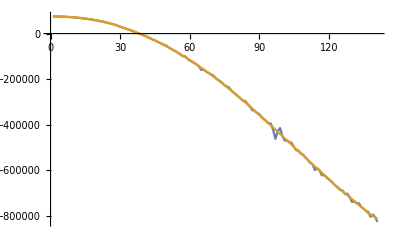

```mathematica
ListLinePlot[{Redata[[1]],Re[mpionT30]}]
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

```mathematica
Export["./RedataT100mu250.dat",Redata]
```

./RedataT100mu250.dat

```mathematica
omega=Table[i,{i,1,701,5}];
ps=Table[i,{i,1,501,5}];
```

```mathematica
Export["./omega.dat",omega];
Export["./ps.dat",ps]
```

./ps.dat